## Problem 1-5: Lasers

### Part B: Expression for Heat Capacity

```mathematica
k=1.38*10^-23(*m^2 kg s^-2 K^-1*)
```

1.38×10^-23

```mathematica
Clear[k]
```

```mathematica
averageE[T_,deltaE_]:=2*deltaE*ⅇ^(-deltaE/(k*T))/(1+2 ⅇ^(-deltaE/(k*T)))
```

```mathematica
D[averageE[T,deltaE],T]
```

-(4 deltaE^2 ⅇ^(-(2 deltaE)/(k T)))/((1+2 ⅇ^(-deltaE/(k T)))^2 k T^2)+(2 deltaE^2 ⅇ^(-deltaE/(k T)))/((1+2 ⅇ^(-deltaE/(k T))) k T^2)

```mathematica
heatCapacity[T_,deltaE_,k_]:=-(4 deltaE^2 ⅇ^(-(2 deltaE)/(k T)))/((1+2 ⅇ^(-deltaE/(k T)))^2 k T^2)+(2 deltaE^2 ⅇ^(-deltaE/(k T)))/((1+2 ⅇ^(-deltaE/(k T))) k T^2)
```

```mathematica
Simplify[heatCapacity[T,deltaE,1]]
```

(2 deltaE^2 ⅇ^(deltaE/T))/((2+ⅇ^(deltaE/T))^2 T^2)

```mathematica
heatCapacity[T,1,1]
```

-(4 ⅇ^(-2/T))/((1+2 ⅇ^(-1/T))^2 T^2)+(2 ⅇ^(-1/T))/((1+2 ⅇ^(-1/T)) T^2)

### Part C: Plot Heat Capacity + Describe What Happens After Temperature

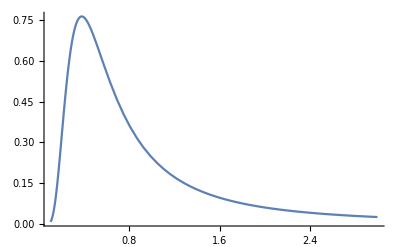

```mathematica
Plot[heatCapacity[T,1,1],{T,0.1,3},PlotRange->All]
```

```mathematica
N[1/Log[2]]
```

1.4427

## Problem 3-4: Phase Diagram of Sulfur

### Part D:

```mathematica
pressure[T_]:=10^(8.5375-0.289524T+0.00154762 T^2)
```

```mathematica
pressure[100]
```

0.000011516

```mathematica
pressure[110]
```

0.0000260653

```mathematica
deltavapH[Tone_,Ttwo_,Pone_,Ptwo_]:=R*Log[Ptwo/Pone]*((Ttwo*Tone)/(Ttwo-Tone))
```

```mathematica
R=8.314 (*J K^-1 mol^-1*);
T1=100+273; (*K*)
P1=pressure[100](*pressure in bar at 100˚C*);
T2=110+273; (*K*);
P2=pressure[110](*an arbitrary pressure in bar for comparison at 110˚C*);
```

```mathematica
deltavapH[100.1+273.15,100+273.15,pressure[100.1],pressure[100]]
```

53738.6

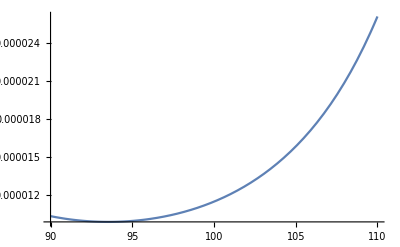

```mathematica
Plot[pressure[T],{T,90,110}]
```

This is not the number the answer key says, which is 3610 kJ/mol

```mathematica
(D[Log[pressure[T]],T]*R*(100+273.15)^2)/.T->(100+273.15)
```

2.30697×10^6